```mathematica
χ05 = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/le_0.5.csv"]][[2;;-1, ;;]];
```

```mathematica
dos05 = Graphics[Import["/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig3/dos_0.5.svg"], ImageSize->{140}]
```

-Graphics-

```mathematica
fig3a = Show[ListDensityPlot[Take[χ05,{1,Length[χ05],3}], ColorFunction->ColorData["DeepSeaColors"],FrameTicks->{{{-1,1},None},{{-2,2},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},Ticks->{0.1,0.7},LabelStyle->{FontFamily->"Times New Roman",16,Black}], Right], PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, Epilog->{Inset[dos05,{.9, -0.5}],Inset[Style["DOS", FontSize->16, FontFamily->"Times", Black], {1., -.15}]},ImageSize->{295, Automatic}, AspectRatio->1],ListPlot[List /@ {{2.2,.3}},PlotMarkers->{Graphics3D[{RGBColor[1,1,1,0],Sphere[]},Boxed->False],6}]]
```

-Graphics-

```mathematica
idosall05= ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/idos_0.5.csv"]][[2;;-1, ;;]];
idosdetail05 = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/idos_detailed_0.5.csv"]][[2;;-1, ;;]];
```

```mathematica
model05=NonlinearModelFit[idosdetail05[[90;;-30]], A(0.52463-x)^k+B,{{A, 1.}, {k, -0.5},{B, 0.}},x];
α05 = k/.model05["BestFitParameters"]
```

-0.499997

```mathematica
model05[x]
```

0.0233812+0.0880019/(0.52463-x)^0.499997

```mathematica
idosdetail05[[-27]]
```

{0.524,4.43774}

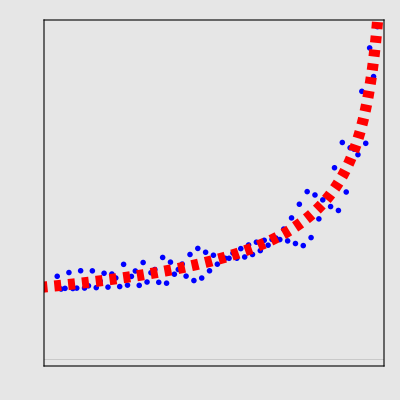

```mathematica
fitb = Show[ListPlot[idosdetail05[[90;;-30]](*idosdetail05[[70;;-27]]*), PlotTheme->"Scientific", PlotRange->{All, All},FrameTicks->None, ImageSize->{80}, AspectRatio->1, PlotMarkers->{"OpenMarkers",2},PlotStyle->Blue],(*ListPlot[idosdetail05[[90;;-30]], PlotStyle->{Blue,PointSize[.02]}], *)Plot[model05[x], {x, 0.35, 0.5246},PlotStyle->{Red,Dashed, Thickness[0.02]}, PlotRange->All],Background->GrayLevel[0.9,0.9]]
```

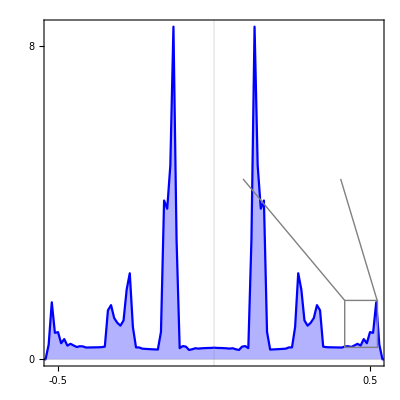

```mathematica
fig3b = Show[ListLinePlot[idosall05, PlotTheme->"Scientific", PlotStyle->{Blue},Filling->Bottom,PlotRange->{{-0.524, 0.524}, All}, AspectRatio->1, ImageSize->{290}, FrameTicks->{{{0,8},None},{{-0.5,0.5},None}},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},Epilog->{Inset[fitb, {0.25, 6}]}],
Graphics[{GrayLevel[0.5],Line[{{0.419, 0.3025}, {0.419, 1.5},{0.524, 1.5},{0.524,0.3025},{0.419, 0.3025}}]}],Graphics[{GrayLevel[0.5],Line[{{0.523, 1.5}, {0.406, 4.6}}]}],Graphics[{GrayLevel[0.5],Line[{{0.419, 1.5}, {0.093, 4.6}}]}]]
```

```mathematica
χ25 = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/le_2.5.csv"]][[2;;-1, ;;]];
```

```mathematica
dos25 = Graphics[Import["/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig3/dos_2.5.svg"], ImageSize->{140}]
```

-Graphics-

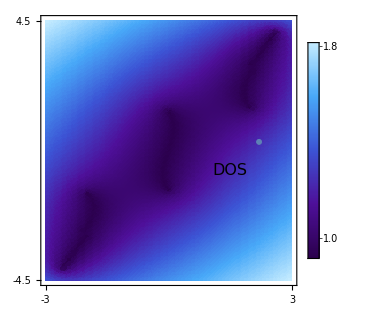

```mathematica
fig3c = Show[ListDensityPlot[Take[χ25,{1,Length[χ25],27}], ColorFunction->ColorData["DeepSeaColors"],InterpolationOrder->0,FrameTicks->{{{-4.5,4.5},None},{{-3,3},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},Ticks->{1.0, 1.8},LabelStyle->{FontFamily->"Times New Roman",16,Black}], Right], PlotRangePadding->None,PlotRange->{{-3,3},{-4.5,4.5},All},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},Epilog->{Inset[dos25,{1.35, -2.25}],Inset[Style["DOS", FontSize->16, FontFamily->"Times", Black], {1.5, -.675}]}, ImageSize->{312, Automatic}, AspectRatio->1],ListPlot[List /@ {{2.2,.3}},PlotMarkers->{Graphics3D[{RGBColor[1,1,1,0],Sphere[]},Boxed->False],6}]]
```

```mathematica
idosall25= ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/idos_2.5.csv"]][[2;;-1, ;;]];
idosdetail25 = ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig3/idos_detailed_2.5.csv"]][[2;;-1, ;;]];
```

```mathematica
model25=NonlinearModelFit[idosdetail25[[500;;629]], A(4.130362-x)^k+B,{{A, 1.}, {k, -0.5},{B, 0.}},x];
α25 = k/.model25["BestFitParameters"]
```

-0.5

```mathematica
model25[x]
```

0.0215836+0.0990953/(4.13036-x)^0.5

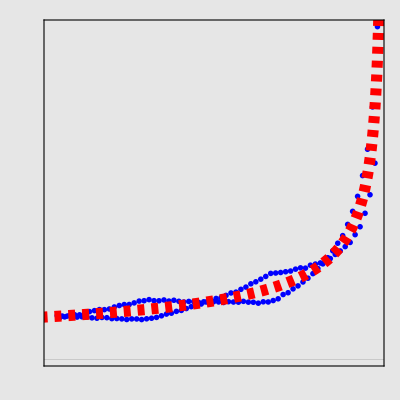

```mathematica
fitd = Show[ListPlot[idosdetail25[[500;;629]](*idosdetail25[[300;;631]]*), PlotTheme->"Scientific", PlotRange->{All, All},FrameTicks->None, ImageSize->{80}, AspectRatio->1, PlotMarkers->{"OpenMarkers",2}, PlotStyle->Blue],(*ListPlot[idosdetail25[[500;;629]], PlotStyle->{Blue,PointSize[.02]}], *)Plot[model25[x], {x, 3.5, 4.131},PlotStyle->{Red,Dashed, Thickness[0.02]}, PlotRange->All],Background->GrayLevel[0.9,0.9]]
```

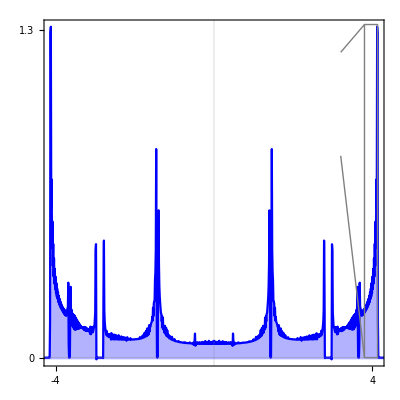

```mathematica
fig3d = Show[ListLinePlot[idosall25, PlotTheme->"Scientific", PlotRange->{{-4.128, 4.128}, All}, AspectRatio->1, ImageSize->{294}, FrameTicks->{{{0,1.3},None},{{-4,4},None}},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},PlotStyle->{Blue},Filling->Bottom,Epilog->{Inset[fitd, {2, 1}]}],Graphics[{GrayLevel[0.5],Line[{{3.8, 0}, {3.8, 1.32},{4.13, 1.32},{4.13, 0},{3.8, 0}}]}],Graphics[{GrayLevel[0.5],Line[{{3.8, 0}, {3.2, .8}}]}],Graphics[{GrayLevel[0.5],Line[{{3.8, 1.32}, {3.2, 1.21}}]}]]
```

```mathematica
Fig3 = ListPlot[{{0,0}},PlotStyle->Opacity[0],PlotRange->{{0,1},{0,1}},ImageSize->{660,Automatic},Axes->None,Epilog->{Inset[fig3a,{.29,0.748}], Inset[fig3b,{.785,0.742}],Inset[fig3c,{.28,0.248}],Inset[fig3d,{.77,0.242}],Inset[Rotate[Row[{Style["Im ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.04,0.76}],Inset[Rotate[Row[{Style["Im ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}],Pi/2],{0.04,0.26}],Inset[Rotate[Row[{Style["ρ(Im ",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}],Pi/2],{0.57,0.26}], Inset[Rotate[Row[{Style["ρ(Im ",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}],Pi/2],{0.57,0.76}],   Inset[Row[{Style["Re ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.255, 0.015}],Inset[Row[{Style["Re ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.255, 0.516}],Inset[Row[{Style["Im ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.795, 0.515}],Inset[Row[{Style["Im ",23,FontFamily->"Times"],Style["E",23,FontFamily->"Times",Italic]}], {0.795, 0.016}],Inset[Row[{Style["γ(",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}], {0.5, 0.93}],Inset[Row[{Style["γ(",23,FontFamily->"Times"],Style["E)",23,FontFamily->"Times",Italic]}], {0.5, 0.43}],Inset[Style["(a)",27,FontFamily->Times],{.095,0.955}],Inset[Style["(c)",27,FontFamily->Times],{.095,0.455}],Inset[Style["(b)",27,FontFamily->Times],{.625,0.955}],Inset[Style["(d)",27,FontFamily->Times],{.625,0.455}]}, AspectRatio->.9]
```

-Graphics-

```mathematica
Export["/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig3/Fig3.pdf",Fig3,"PDF"]
```

/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig3/Fig3.pdf